```mathematica
a = 2;
k = 1.0;
Clear[a,b, k, aa,bb,cc]
b = a;
a = 2;
u = Sin[Pi*x*a] * Cos[Pi*y*b]
dux =  D[u, x]
duy = D[u, y]
```

Cos[2 π y] Sin[2 π x]

2 π Cos[2 π x] Cos[2 π y]

-2 π Sin[2 π x] Sin[2 π y]

```mathematica
k = aa +bb*u + cc *u*u
Clear [k]
qx = - dux * k
qy = - duy * k
f = D[qx, x] + D[qy, y]
```

aa+bb Cos[2 π y] Sin[2 π x]+cc Cos[2 π y]^2 Sin[2 π x]^2

-2 k π Cos[2 π x] Cos[2 π y]

2 k π Sin[2 π x] Sin[2 π y]

8 k π^2 Cos[2 π y] Sin[2 π x]

```mathematica
FullSimplify[qx]
FullSimplify[qy]
```

-a π Cos[a π x] Cos[a π y] (aa+Cos[a π y] Sin[a π x] (bb+cc Cos[a π y] Sin[a π x]))

a π Sin[a π x] (aa+Cos[a π y] Sin[a π x] (bb+cc Cos[a π y] Sin[a π x])) Sin[a π y]

```mathematica
FullSimplify[f]
```

1/8 a^2 π^2 (-4 bb Cos[2 a π x]+4 bb (1-2 Cos[2 a π x]) Cos[2 a π y]-2 (-8 aa+cc+5 cc Cos[2 a π x]) Cos[a π y] Sin[a π x]+cc Cos[3 a π y] (5 Sin[a π x]-3 Sin[3 a π x]))

```mathematica
a = 2.0;
aa = 1.0;
bb = 0.0;
cc= 0.0;
```

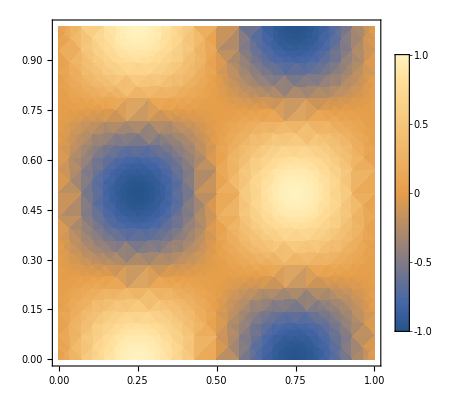

```mathematica
DensityPlot[u,{x,0,1},{y,0,1},PlotTheme->"Detailed"]
```

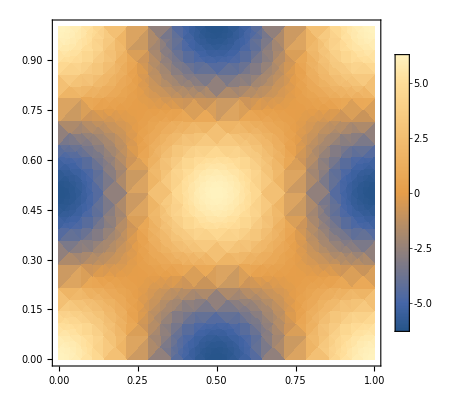

```mathematica
DensityPlot[dux,{x,0,1},{y,0,1},PlotTheme->"Detailed"]
```

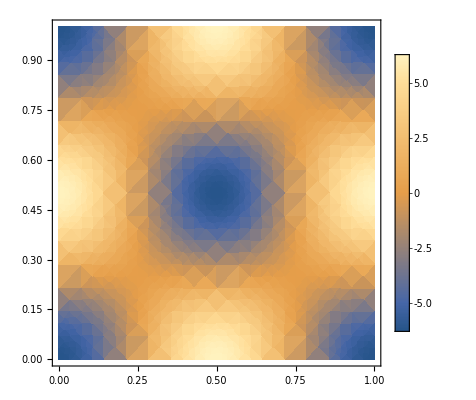

```mathematica
DensityPlot[qx,{x,0,1},{y,0,1},PlotTheme->"Detailed"]
```